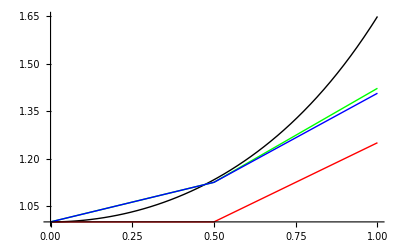

```mathematica
(*diff eq*)
f[x_,u_]:=x*u;

(*derivatives for use with Taylor approx*)
df[x_,u_]:=u+x*f[x,u];

(*mesh parameter*)
Δx=.5;

(*initial value*)
xnow=0;
unow=1;
urnow=1;
utnow=1;

(*approximation data*)
recordeuler={{xnow,unow}};
recordrunge={{xnow,unow}};
recordtaylor={{xnow,unow}};

While[xnow<1,
xnext=xnow+Δx;

unext=unow+f[xnow,unow]*Δx;
ξ=(xnext+xnow)/2;
uξ=unow+Δx/2 f[xnow,unow];
urnext=unow+f[ξ,uξ]*Δx;
utnext=unow+f[xnow,unow]*Δx+1/2 df[xnow,unow]*Δx^2;

xnow=xnext;
unow=unext;
urnow=urnext;
utnow=utnext;
AppendTo[recordeuler,{xnow,unow}];
AppendTo[recordrunge,{xnow,urnow}];
AppendTo[recordtaylor,{xnow,utnow}];
]
Show[Plot[E^(.5x^2),{x,0,1},PlotStyle->Black,ImageSize->Full],ListLinePlot[{recordeuler,recordrunge,recordtaylor},PlotStyle->{Red,Green,Blue}]]
```